# Energy Minimisation

everything is done in rescaled coordinates so the energy is E/(A*rho*theta^2)

## The inter layer coupling function

{-(2 π)/3,(2 π)/(√3)}

{-(2 π)/3,-(2 π)/(√3)}

{(4 π)/3,0}

{0,(4 π)/(√3)}

{2 π,-(2 π)/(√3)}

{-2 π,-(2 π)/(√3)}

-Graphics-

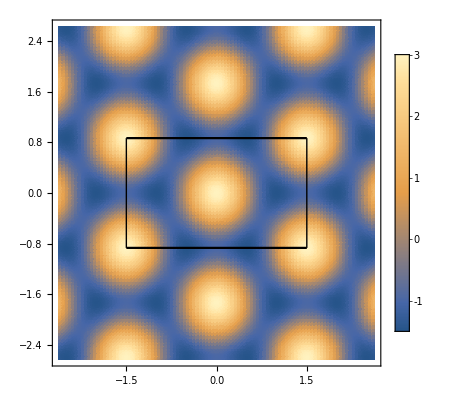

```mathematica
Clear[a,F,x,y,kx,ky]
a=1;
xmax=3*a/(2);
ymax=Sqrt[3]*a/(2);
V=4*ymax*xmax;

q1=2*Pi/a*{-1/3,1/Sqrt[3]}
q2=2*Pi/a*{-1/3,-1/Sqrt[3]}
q3=-(q1+q2)

q2h1=2*q1+q3
q2h2=2*q3+q2
q2h3=2*q2+q1

components={1,1};
rvec=Function[{x,y},{x,y}];

eta=Function[{x,y},Cos[Dot[q1,rvec[x,y]]]+Cos[Dot[q2,rvec[x,y]]]+Cos[Dot[q3,rvec[x,y]]]];
eta2h=Function[{x,y},Cos[Dot[q2h1,rvec[x,y]]]+Cos[Dot[q2h2,rvec[x,y]]]+Cos[Dot[q2h3,rvec[x,y]]]];
J=Function[{delta,x,y},delta*eta[x,y]];

Plot1=DensityPlot[J[1,x,y],{x,-1.75xmax,1.75 xmax},{y,-1.75xmax,1.75 xmax},PlotLegends->Automatic,PlotPoints->100,FrameTicksStyle->20];
DensityPlot[eta2h[x,y],{x,-1.75xmax,1.75 xmax},{y,-1.75xmax,1.75 xmax},PlotLegends->Automatic,PlotPoints->100,FrameTicksStyle->20]
Plot2=Plot[{x=ymax,x=-ymax},{x,-xmax,xmax},PlotStyle->Black,PlotStyle->Thick];
Plot3=Graphics[{Thick,Line[{{-xmax,-ymax},{-xmax,ymax}}],Line[{{xmax,-ymax},{xmax,ymax}}]}];

Show[Plot1,Plot2,Plot3]
DensityPlot[J[1,x,y],{x,-xmax,xmax},{y,-ymax,ymax},PlotLegends->Automatic,PlotPoints->100];
leg1=BarLegend[{"BeachColors",{-1,3}},LabelStyle->Directive[FontSize->20]]
```

check lengths of vectors should be same

```mathematica
Total[q1^2]
Total[q2^2]
Total[q3^2]
```

(16 π^2)/9

(16 π^2)/9

(16 π^2)/9

## The Energy Functional

```mathematica
phiS=Function[{phiS0,phiS1,phiS2,x,y},phiS0+phiS1*eta[x,y]+eta2h[x,y]*phiS2];
phiA=Function[{phiA0,phiA1,phiA2,x,y},phiA0+phiA1*eta[x,y]+eta2h[x,y]*phiA2];

phi1=Function[{A0,A1,A2,S0,S1,S2,x,y},1/2*(phiS[S0,S1,S2,x,y]+phiA[A0,A1,A2,x,y])];
phi2=Function[{A0,A1,A2,S0,S1,S2,x,y},1/2*(phiS[S0,S1,S2,x,y]-phiA[A0,A1,A2,x,y])];

gradsq=Function[{phiS1,phiA1,phiS2,phiA2},3/8 *(Norm[q1]^2*((phiS1)^2+(phiA1)^2)+Norm[q2h1]^2*((phiS2)^2+(phiA2)^2))];

CosA=Function[{phiA0,phiA1,phiA2,x,y},Cos[phiA[phiA0,phiA1,phiA2,x,y]]];
Nlzsq=Function[{phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y},Cos[phiS[phiS0,phiS1,phiS2,x,y]]*Cos[phiS[phiA0,phiA1,phiA2,x,y]]+1];

Integrand=Function[{d,delta,phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y},-d*Nlzsq[phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y]-J[delta,x,y]*CosA[phiA0,phiA1,phiA2,x,y]];

Energy=Function[{d,delta,phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y},1/V*(gradsq[phiS1,phiA1,phiS2,phiA2]+NIntegrate[Integrand[d,delta,phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y],{x,-xmax,xmax},{y,-ymax,ymax}])];
```

```mathematica
Energy minimisation
```

```mathematica
minimisation=Function[{indelta,ind,inphiS0,inphiS1,inphiS2,inphiA0,inphiA1,inphiA2,acceptno,step,Estep,inT,avsmall},

d=ind/(1-ind);
delta=indelta/(1-indelta);

phiS0=inphiS0;
phiS1=inphiS1;
phiS2=inphiS2;
phiA0=inphiA0;
phiA1=inphiA1;
phiA2=inphiA2;

beta=1/inT;


Eold=Energy[d,delta,phiS0,phiS1,phiS2,phiA0,phiA1,phiA2,x,y];
Enew=Eold+5;

Eiters={};
S0iters={phiS0};
S1iters={phiS1};
S2iters={phiS2};
A0iters={phiA0};
A1iters={phiA1};
A2iters={phiA2};
niters={0};
n=0;
accept=0;
acceptiters={accept};


While[Abs[Eold-Enew]>0,
n=n+1;


DeltaphiS0=phiS0+RandomReal[{-step,step}];
DeltaphiS1=phiS1+RandomReal[{-step,step}];
DeltaphiS2=phiS2+RandomReal[{-step,step}];
DeltaphiA0=phiA0+RandomReal[{-step,step}];
DeltaphiA1=phiA1+RandomReal[{-step,step}];
DeltaphiA2=phiA2+RandomReal[{-step,step}];

Enew=Energy[d,delta,DeltaphiS0,DeltaphiS1,DeltaphiS2,DeltaphiA0,DeltaphiA1,DeltaphiA2,x,y];
p=Exp[-beta*(Enew-Eold)];
probability=Min[1,p];
random=RandomReal[];
If[ probability>random,{phiS0=DeltaphiS0,phiS1=DeltaphiS1,phiS2=DeltaphiS2,phiA0=DeltaphiA0,phiA1=DeltaphiA1, phiA2=DeltaphiA2,If[Eold<Enew,accept=accept+1],Eold=Enew,Enew=2*Eold}];

If[ Mod[n,Estep]==0,{Eiters=Append[Eiters,Eold],S0iters=Append[S0iters,phiS0],S1iters=Append[S1iters,phiS1],S2iters=Append[S2iters,phiS2],A0iters=Append[A0iters,phiA0],A1iters=Append[A1iters,phiA1],A2iters=Append[A2iters,phiA2],niters=Append[niters,n],acceptiters=Append[acceptiters,accept]}];


If[accept==acceptno,{Eold=0,Enew=0}]];

len=Length[Eiters];
If[len<50,average=avsmall];
If[50<len<75,average=2*avsmall];
If[len>75,average=3*avsmall];
Ef=Mean[Eiters[[-average;;]]];
S0=Mean[S0iters[[-average;;]]];
S1=Mean[S1iters[[-average;;]]];
S2=Mean[S2iters[[-average;;]]];
A0=Mean[A0iters[[-average;;]]];						
A1=Mean[A1iters[[-average;;]]];
A2=Mean[A2iters[[-average;;]]]
];
```

Getting the data

0.66

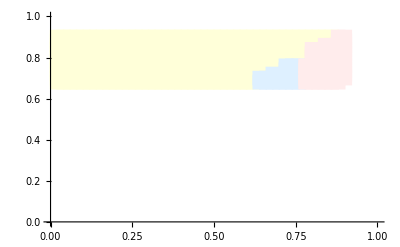

0.02

General::munfl: Exp[-724.138] is too small to represent as a normalized machine number; precision may be lost.

Part::span: -average;;All is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

0.04

0.06

0.08

0.1

0.12

General::munfl: Exp[-732.935] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.64

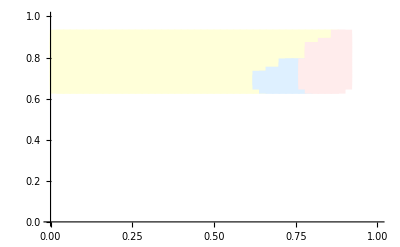

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.62

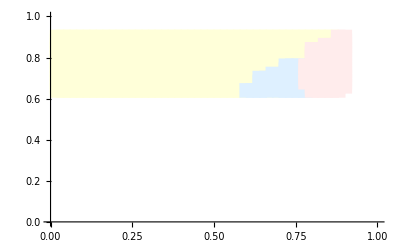

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.6

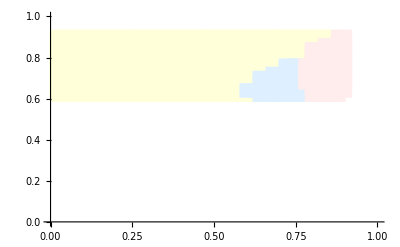

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.58

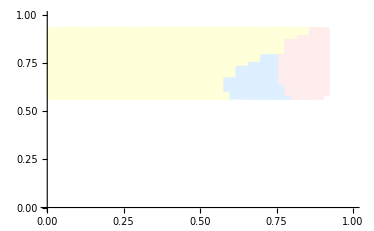

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.56

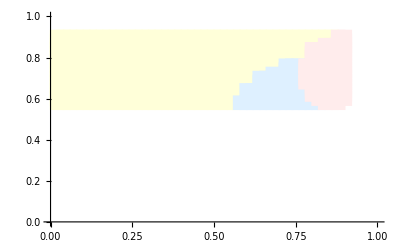

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.54

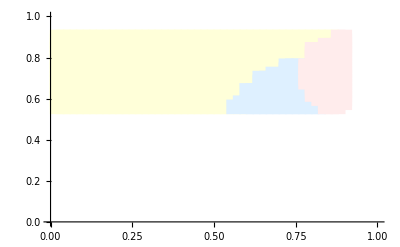

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.52

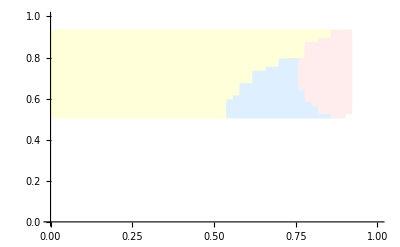

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000143124 and 6.43719×10^-11 for the integral and error estimates.

0.88

0.9

0.5

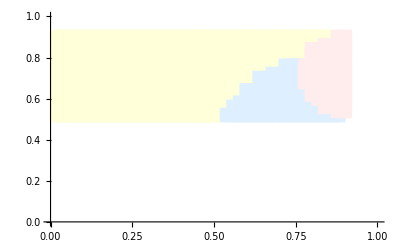

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.48

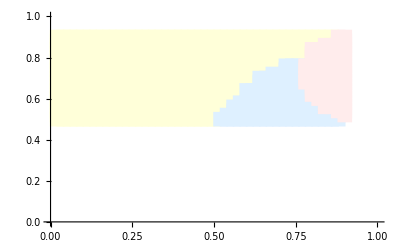

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.46

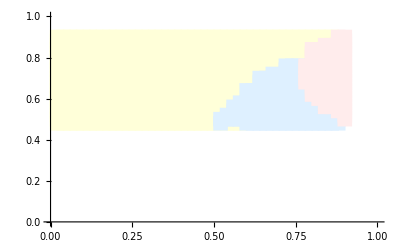

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.44

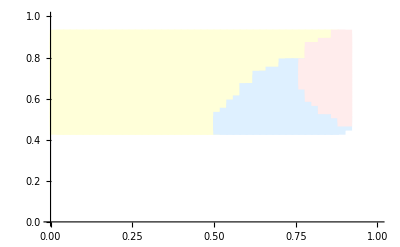

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.42

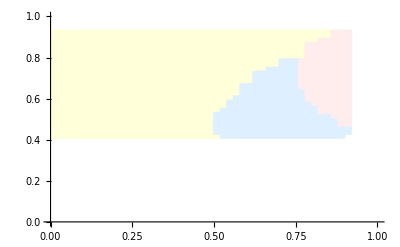

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.4

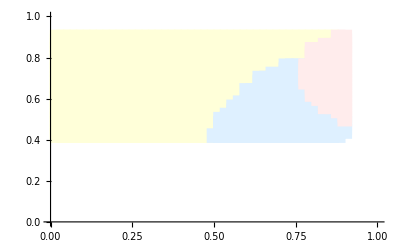

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.38

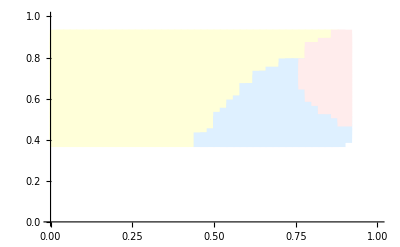

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.36

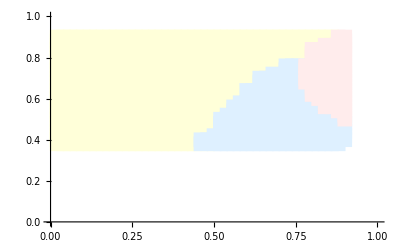

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.34

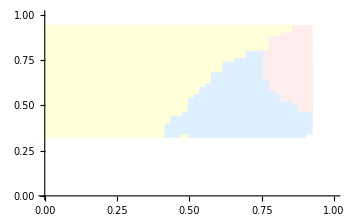

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000113429 and 1.50573×10^-10 for the integral and error estimates.

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.32

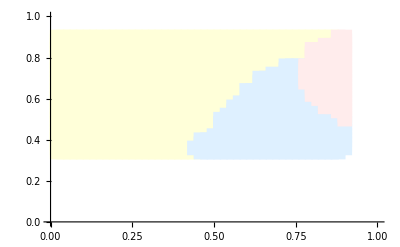

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.3

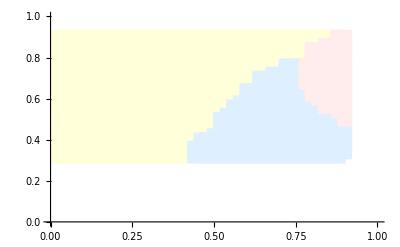

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.28

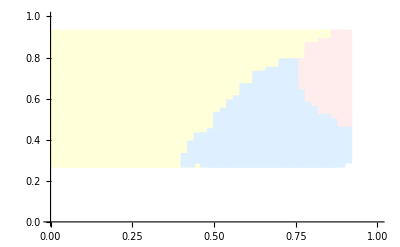

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000794012 and 1.00147×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.26

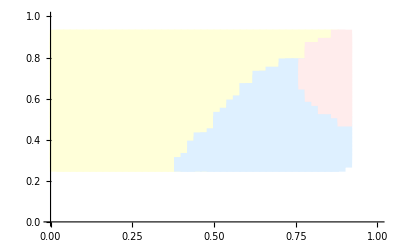

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.24

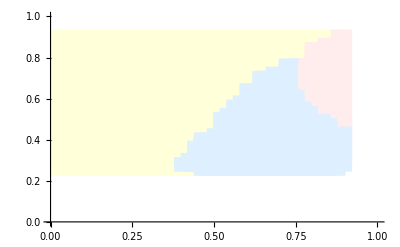

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.22

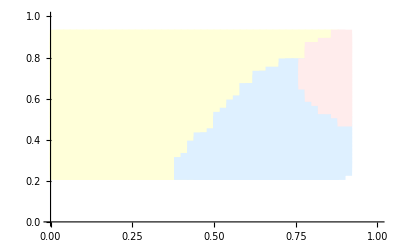

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.2

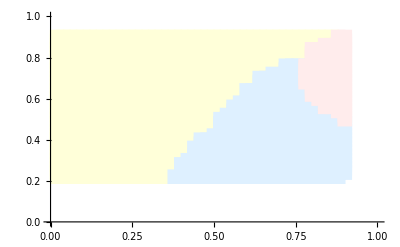

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.18

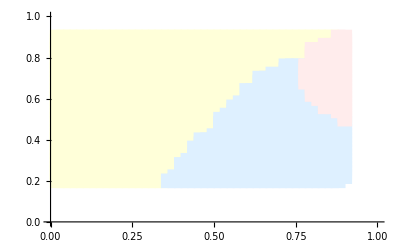

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.16

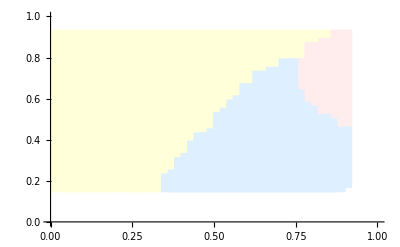

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.14

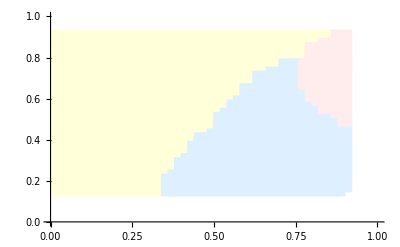

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.12

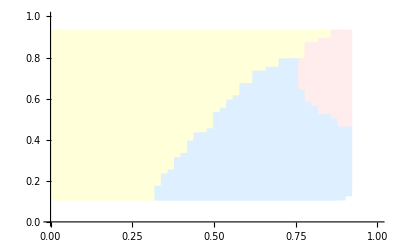

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.1

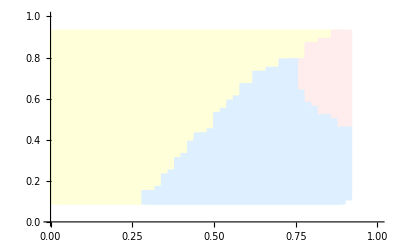

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.08

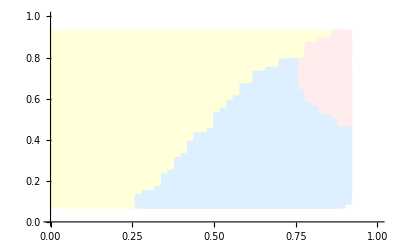

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.06

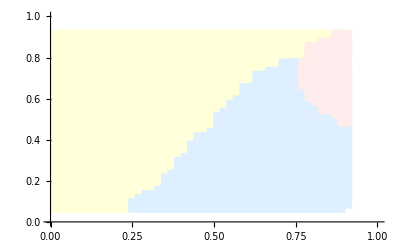

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.04

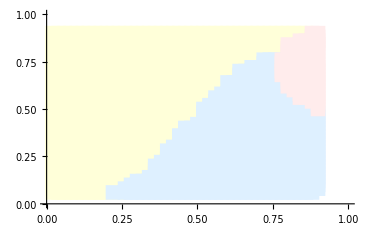

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

0.02

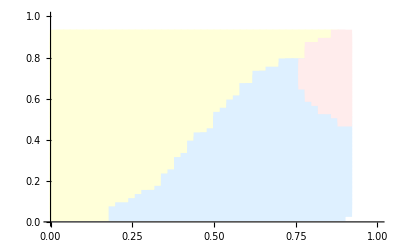

0.02

0.04

0.06

0.08

0.1

0.12

0.14

0.16

0.18

0.2

0.22

0.24

0.26

0.28

0.3

0.32

0.34

0.36

0.38

0.4

0.42

0.44

0.46

0.48

0.5

0.52

0.54

0.56

0.58

0.6

0.62

0.64

0.66

0.68

0.7

0.72

0.74

0.76

0.78

0.8

0.82

0.84

0.86

0.88

0.9

```mathematica
For[ind=0.66,ind>0.01,ind=ind-0.02,{Print[ind],

SetDirectory[NotebookDirectory[]],
Export["S0list",S0list,"List"],
Export["A0list",A0list,"List"],
Export["S1list",S1list,"List"],
Export["A1list",A1list,"List"],
Export["S2list",S2list,"List"],
Export["A2list",A2list,"List"],
Export["Eflist",Eflist,"List"],
Export["dlist",indlist,"List"],
Export["deltalist",indeltalist,"List"],

nS0list={};
nS1list={};
nA0list={};
nA1list={};
Apoints={};
Spoints={};
Cpoints={};

For[n=0,n<Length[S0list],n=n+1,{
If[0.1<Abs[S0list[[n]]]<3,{nS0list=Append[nS0list,n]}],
If[0.1<Abs[S1list[[n]]]<3,nS1list=Append[nS1list,n]],
If[0.1<Abs[A0list[[n]]]<3,nA0list=Append[nA0list,n]],
If[0.1<Abs[A1list[[n]]]<3,nA1list=Append[nA1list,n]],
If[0.1<Abs[S1list[[n]]]<3,Apoints=Append[Apoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1<Abs[A1list[[n]]]<3 && 0.1>Abs[S1list[[n]]],Spoints=Append[Spoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1>Abs[A1list[[n]]]||Abs[A1list[[n]]]>3,Cpoints=Append[Cpoints,{indeltalist[[n]],indlist[[n]]}]]}];

plotc=ListPlot[Cpoints,PlotMarkers->{"■",15},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",15},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",15},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotc,plots,plota},BaseStyle->{FontSize->18}]],

For[indelta=0.02,indelta<0.91,indelta=indelta+0.02,{Print[indelta],
	indlist=Append[indlist,ind],
	indeltalist=Append[indeltalist,indelta],
	minimisation[indelta,ind,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,3000,Pi/100,1000,0.001,20],
	Eflist=Append[Eflist,Ef],
	S0list=Append[S0list,S0],
	S1list=Append[S1list,S1],
	S2list=Append[S2list,S2],
	A0list=Append[A0list,A0],
	A1list=Append[A1list,A1],
	A2list=Append[A2list,A2]}]}]
```

0.78

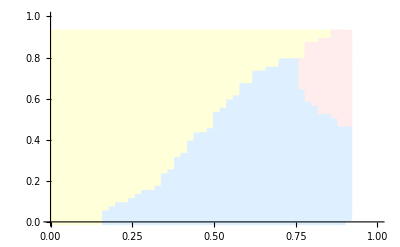

0.72

0.74

0.76

0.78

General::munfl: Exp[-757.62] is too small to represent as a normalized machine number; precision may be lost.

0.8

0.82

0.84

General::munfl: Exp[-743.951] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-788.769] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.86

0.88

0.9

```mathematica
For[ind=0.78,ind>0.77,ind=ind-0.02,{Print[ind],

SetDirectory[NotebookDirectory[]],
Export["S0list",S0list,"List"],
Export["A0list",A0list,"List"],
Export["S1list",S1list,"List"],
Export["A1list",A1list,"List"],
Export["S2list",S2list,"List"],
Export["A2list",A2list,"List"],
Export["Eflist",Eflist,"List"],
Export["dlist",indlist,"List"],
Export["deltalist",indeltalist,"List"],

nS0list={};
nS1list={};
nA0list={};
nA1list={};
Apoints={};
Spoints={};
Cpoints={};

For[n=0,n<Length[S0list],n=n+1,{
If[0.1<Abs[S0list[[n]]]<3,{nS0list=Append[nS0list,n]}],
If[0.1<Abs[S1list[[n]]]<3,nS1list=Append[nS1list,n]],
If[0.1<Abs[A0list[[n]]]<3,nA0list=Append[nA0list,n]],
If[0.1<Abs[A1list[[n]]]<3,nA1list=Append[nA1list,n]],
If[0.1<Abs[S1list[[n]]]<3,Apoints=Append[Apoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1<Abs[A1list[[n]]]<3 && 0.1>Abs[S1list[[n]]],Spoints=Append[Spoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1>Abs[A1list[[n]]]||Abs[A1list[[n]]]>3,Cpoints=Append[Cpoints,{indeltalist[[n]],indlist[[n]]}]]}];

plotc=ListPlot[Cpoints,PlotMarkers->{"■",15},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",15},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",15},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Print[Show[{plotc,plots,plota},BaseStyle->{FontSize->18}]],

For[indelta=0.72,indelta<0.91,indelta=indelta+0.02,{Print[indelta],
	indlist=Append[indlist,ind],
	indeltalist=Append[indeltalist,indelta],
	minimisation[indelta,ind,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,3000,Pi/100,1000,0.001,20],
	Eflist=Append[Eflist,Ef],
	S0list=Append[S0list,S0],
	S1list=Append[S1list,S1],
	S2list=Append[S2list,S2],
	A0list=Append[A0list,A0],
	A1list=Append[A1list,A1],
	A2list=Append[A2list,A2]}]}]
```

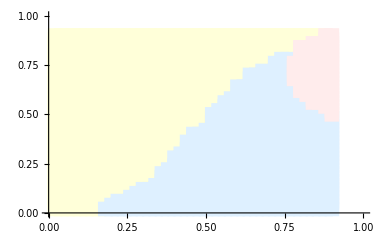

```mathematica
nS0list={};
nS1list={};
nA0list={};
nA1list={};
Apoints={};
Spoints={};
Cpoints={};

For[n=0,n<=Length[S0list],n=n+1,{
If[0.1<Abs[S0list[[n]]]<3,{nS0list=Append[nS0list,n]}],
If[0.1<Abs[S1list[[n]]]<3,nS1list=Append[nS1list,n]],
If[0.1<Abs[A0list[[n]]]<3,nA0list=Append[nA0list,n]],
If[0.1<Abs[A1list[[n]]]<3,nA1list=Append[nA1list,n]],
If[0.1<Abs[S1list[[n]]]<3,Apoints=Append[Apoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1<Abs[A1list[[n]]]<3 && 0.1>Abs[S1list[[n]]],Spoints=Append[Spoints,{indeltalist[[n]],indlist[[n]]}]],
If[0.1>Abs[A1list[[n]]]||Abs[A1list[[n]]]>3,Cpoints=Append[Cpoints,{indeltalist[[n]],indlist[[n]]}]]}];

plotc=ListPlot[Cpoints,PlotMarkers->{"■",15},PlotStyle->{LightYellow},PlotRange->{{0,1},{0,1}}];
plota=ListPlot[Apoints,PlotMarkers->{"■",15},PlotStyle->{LightPink},PlotRange->{{0,1},{0,1}}];
plots=ListPlot[Spoints,PlotMarkers->{"■",15},PlotStyle->{LightBlue},PlotRange->{{0,1},{0,1}}];
Show[{plotc,plots,plota},BaseStyle->{FontSize->18}]
```

```mathematica
Length[S0list]
```

2025

```mathematica
Length[S1list]
```

2025

```mathematica
Length[indlist]
```

2025

```mathematica
Sqrt[2025]
```

45

```mathematica
SetDirectory[NotebookDirectory[]]
Export["S0list",S0list,"List"]
Export["A0list",A0list,"List"]
Export["S1list",S1list,"List"]
Export["A1list",A1list,"List"]
Export["S2list",S2list,"List"]
Export["A2list",A2list,"List"]
Export["Eflist",Eflist,"List"]
Export["dlist",indlist,"List"]
Export["deltalist",indeltalist,"List"]
```

/Users/abigailpickering/Documents/year 4/Masters Project/Mathematica/High resolution phase plot/Attempt 4

S0list

A0list

S1list

A1list

S2list

A2list

Eflist

dlist

deltalist